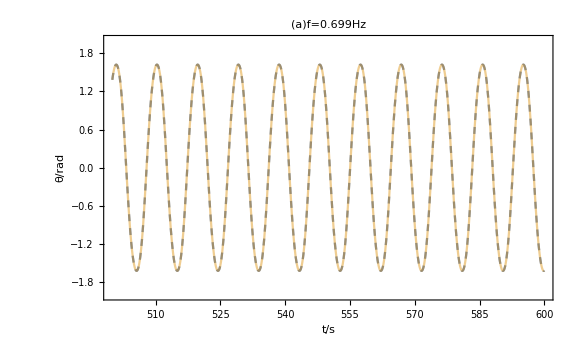

```mathematica
Module[{δ,ω0,ωd,f0},
δ=0.25;
ω0=1;
ωd=0.6667;
f0=0.699;
Plot[Evaluate@{
NDSolveValue[{θ''[t]+2δ θ'[t]+ω0^2 Sin[θ[t]]==f0 Cos[ωd t],θ[0]==0.001,θ'[0]==0.2},θ[t],{t,500,600}],NDSolveValue[{θ''[t]+2δ θ'[t]+ω0^2 Sin[θ[t]]==f0 Cos[ωd t],θ[0]==0,θ'[0]==0.2},θ[t],{t,500,600}]},{t,500,600},
PlotRange->{{500,600},{-2,2}},
Frame->True,
FrameLabel->{"t/s","θ/rad"},
PlotLabel->"(a)f=0.699Hz",PlotStyle->{Dashed, Opacity[0.5]}
]
]
```

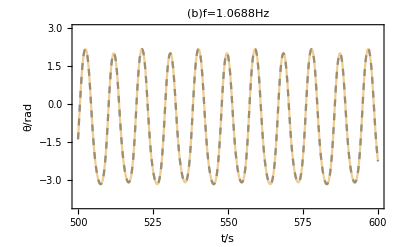

```mathematica
Module[{δ,ω0,ωd,f0},
δ=0.25;
ω0=1;
ωd=0.6667;
f0=1.0688;
Plot[Evaluate@{
NDSolveValue[{θ''[t]+2δ θ'[t]+ω0^2 Sin[θ[t]]==f0 Cos[ωd t],θ[0]==0.001,θ'[0]==0.2},θ[t],{t,500,600}],NDSolveValue[{θ''[t]+2δ θ'[t]+ω0^2 Sin[θ[t]]==f0 Cos[ωd t],θ[0]==0,θ'[0]==0.2},θ[t],{t,500,600}]},{t,500,600},
PlotRange->{{500,600},{-4,3}},
Frame->True,
FrameLabel->{"t/s","θ/rad"},
PlotLabel->"(b)f=1.0688Hz",PlotStyle->{Dashed, Opacity[0.5]}
]
]
```

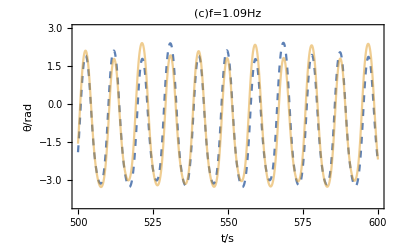

```mathematica
Module[{δ,ω0,ωd,f0},
δ=0.25;
ω0=1;
ωd=0.6667;
f0=1.09;
Plot[Evaluate@{
NDSolveValue[{θ''[t]+2δ θ'[t]+ω0^2 Sin[θ[t]]==f0 Cos[ωd t],θ[0]==0.001,θ'[0]==0.2},θ[t],{t,500,600}],NDSolveValue[{θ''[t]+2δ θ'[t]+ω0^2 Sin[θ[t]]==f0 Cos[ωd t],θ[0]==0,θ'[0]==0.2},θ[t],{t,500,600}]},{t,500,600},
PlotRange->{{500,600},{-4,3}},
Frame->True,
FrameLabel->{"t/s","θ/rad"},
PlotLabel->"(c)f=1.09Hz",PlotStyle->{Dashed, Opacity[0.5]}
]
]
```

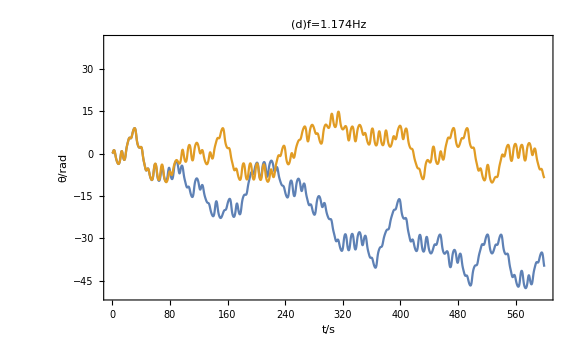

```mathematica
Module[{δ,ω0,ωd,f0},
δ=0.25;
ω0=1;
ωd=0.6667;
f0=1.174;
Plot[Evaluate@{
NDSolveValue[{θ''[t]+2δ θ'[t]+ω0^2 Sin[θ[t]]==f0 Cos[ωd t],θ[0]==0.001,θ'[0]==0.2},θ[t],{t,0,600}],NDSolveValue[{θ''[t]+2δ θ'[t]+ω0^2 Sin[θ[t]]==f0 Cos[ωd t],θ[0]==0,θ'[0]==0.2},θ[t],{t,0,600}]},{t,0,600},
PlotRange->{{0,600},{-50,40}},
Frame->True,
FrameLabel->{"t/s","θ/rad"},
PlotLabel->"(d)f=1.174Hz"
]
](*这个图和书上的出入较大，不知为何*)
```